# px5503 - Data Visualisation 9 - Multiple plots

## Plots with multiple panels

The following code illustrates how we can gather a number of plots into a single, multi-panel plot:

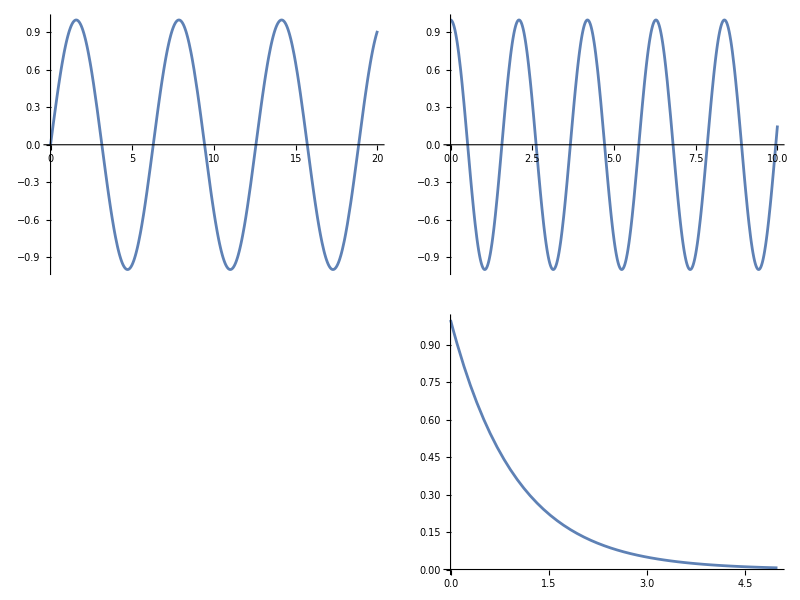

```mathematica
p1=Plot[Sin[x],{x,0,20}];
p2=Plot[Cos[3x],{x,0,10}];
p3=Plot[Exp[-x],{x,0,5},AspectRatio->1.0/4.0];

Graphics[{
Inset[p1,{0,0},{Left,Bottom},1],
Inset[p2,{1,0},{Left,Bottom},1],
Inset[p3,{1,-0.6},{Center,Bottom},1.8],

Style[Text["This is The Title", {0,0.7},{-1,-1}],FontSize->36]
},

ImageSize->Full
]
```

The key is the command Inset, which allows you to place an arbitrary object into a Graphics display. That object could be anything that Mathematica can display, such as an image, or another plot:

 Inset[p1,{0,0},{Left,Bottom},1]
 
 The {0,0} in the code above is the coordinate of the point where the object p1 (a Sine plot in the example above) should be placed. It is important to understand that these coordinates are in the coordinate system of the Graphics display, not in the coordinate system of any of the subplots. It works just like in the custom plots we learned in Notebook 2, except that the objects we are arranging on our canvas are themselves plots.
 
 The {Left,Bottom} directive dictates which position of the plot will be placed at the coordinates we prescribe. In this case, we are saying that the bottom left corner of the image representing the plot will be at coordinate {0,0}.
 
 Finally, the 1 is the size of the inserted plot. As usual, the Graphics will adapt the display to fit all objects within it, so the size is to some extent arbitrary. It is the relative size of all the plots in your panel that you should pay attention to.
 
 Notice the option ImageSize->Full, in Graphics. This is really important, to make sure your plots are sized appropriately. Without it, you will find it hard to control the relative sizes of your subplots, and arrange them they way you want.

### Inset plots

Instead of a panel where we add multiple plots, sometimes we may have a main plot, on top of which we want to add one or more smaller plots - “inset plots”. We do this through the Prolog or Epilog, using again the Inset instruction:

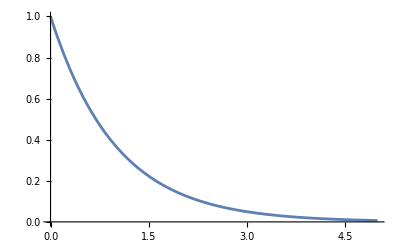

```mathematica
p2=Plot[Cos[3x],{x,0,10}];

Plot[Exp[-x],{x,0,5},
Epilog->{Inset[p2,{2,0.4},{Left,Bottom},2.5]}
]
```

When using Inset in this way,  the coordinate system is that of the surrounding plot - in this example, the exponential plot.

### Controlling the font size

Because the font size scales independently of the plot size, it is a good idea to use variables to control font sizes you want to be the same in all subplots, so that you can rescale them all easily.

```mathematica
tickLabelSize=20;

p1=Plot[Sin[x],{x,0,20},AxesStyle->tickLabelSize];
p2=Plot[Cos[3x],{x,0,10},AxesStyle->tickLabelSize];
p3=Plot[Exp[-x],{x,0,5},AspectRatio->1.0/4.0,AxesStyle->tickLabelSize];

Graphics[{
Inset[p1,{0,0},{Left,Bottom},1],
Inset[p2,{1,0},{Left,Bottom},1],
Inset[p3,{1,-0.6},{Center,Bottom},1.8],

Style[Text["This is The Title", {0,0.7},{-1,-1}],FontSize->36]
},

ImageSize->Full
]
```

-Graphics-

### Arranging plots using images

#### Creating images

You can generate an image from a plot by right-clicking it, and then selecting “Save graphic as...” in the pop-up menu. You can select multiple options for the image format. However, by default, Mathematica typically generates low-resolution images. So a better choice is to generate images using code. For example, let us consider one of the plots in the example:

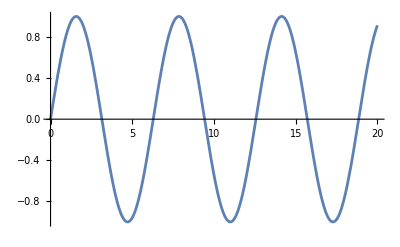

```mathematica
p1
```

We can save it to disk with the code:

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"p1.png"}],p1];
```

This code  saves the plot stored in the variable p1 to the file p1.png, and makes sure that file is in the same folder as the notebook you are working on. Using FileNameJoin makes sure this code works for different operating systems. The image type is determined from the file extension; in this case, it generates a PNG image.

You can import an image using Import:

```mathematica
p1Img=Import[FileNameJoin[{NotebookDirectory[],"p1.png"}]]
```

-Graphics-

If the image resolution is not satisfactory, we can force a higher resolution by magnifying the image:

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"p1.png"}],Magnify[p1,4]];
```

```mathematica
p1Img=Import[FileNameJoin[{NotebookDirectory[],"p1.png"}]]
```

-Graphics-

#### Creating multi-panel plots using images

You can use Inset to use images of plats in order to arrange them into a multi-panel plot, as shown below.

```mathematica
p1=Plot[Sin[x],{x,0,20}];
Export[FileNameJoin[{NotebookDirectory[],"p1.png"}],Magnify[p1,4]];

p2=Plot[Cos[3x],{x,0,10}];
Export[FileNameJoin[{NotebookDirectory[],"p2.png"}],Magnify[p2,4]];

p3=Plot[Exp[-x],{x,0,5},AspectRatio->1.0/4.0];
Export[FileNameJoin[{NotebookDirectory[],"p3.png"}],Magnify[p3,4]];

p1Img=Import[FileNameJoin[{NotebookDirectory[],"p1.png"}]];
p2Img=Import[FileNameJoin[{NotebookDirectory[],"p2.png"}]];
p3Img=Import[FileNameJoin[{NotebookDirectory[],"p3.png"}]];

Graphics[{
Inset[p1Img,{0,0},{Left,Bottom},1],
Inset[p2Img,{1,0},{Left,Bottom},1],
Inset[p3Img,{1,-0.6},{Center,Bottom},1.8],

Style[Text["This is The Title", {0,0.7},{-1,-1}],FontSize->36]
},

ImageSize->Full
]
```

-Graphics-

Notice that the font sizes are now different! This happens because when it generates an image of a plot, Mathematica sometimes changes the font size. This often happens if you set the aspect ratio manually. You have to pay attention to this if you use this method of creating multi-panel plots.

## Designing multi-panel plots

### The same design principles you learned apply to each subplot

Each subplot in a multi-panel plot should follow the same principles we have seen throughout the course: avoid clutter, highlight the important parts, pay attention to aesthetics, to name a few.

### The subplots should be connected by a common thread, and tell a story together

There should be a clear reason you have multiple plots gathered into a single plot: they should be parts of a single, clear message. Often, they should be telling a story together.

### You will need to simplify the subplots

Because of the reduced space each subplot gets compared to a single, dedicated plot, you will typically need to simplify each subplot. When you have a single individual plot, you have more space for inset text, markers, and other features in the plot to help you convey its message. In multi-panel plots, however, each subplot will be significantly smaller, and you may not have enough space for all this. This will result is subplots with fewer features, particularly less inset text and shortened axes labels and tick labels.

### The style should be consistent across subplots

The style should be kept as consistent as possible across the subplots. For example, the fonts, the colours, the thickness of lines, and so on should be the same, unless there is a good reason otherwise.

## Suggestion: design your output (presentation/paper/thesis/report/etc) through the key plots

One way many people plan how to write a data-centric output (meaning a paper, presentation, report, etc) is to first create the key plots that encapsulate your main results and conclusions, and then write the rest around those plots. In a sense, the output could be thought of as something that explains the plots, gives them context, and expounds on their meaning and consequences. This is how many people in the biomedical sciences write papers, and it is a good suggestion for any output of a data-centric project.

## Examples

https://pudding.cool/2017/03/film-dialogue/

-Graphics-

-Graphics-

(https://www.storytellingwithdata.com/blog/its-okay-to-use-multiple-graphs)

-Graphics-

https://www.storytellingwithdata.com/makeovers

-Graphics-

-Graphics-

https://www.storytellingwithdata.com/blog/from-dashboard-to-story

-Graphics-

https://www.storytellingwithdata.com/blog/2017/4/19/numbers-of-different-magnitudes

-Graphics-

https://www.storytellingwithdata.com/blog/2021/1/10/lets-improve-this-graph-yt9xj

-Graphics-

https://pubmed.ncbi.nlm.nih.gov/39425392/

-Graphics-

## Challenges

The following is (hypothetical) data detailing the numbers of papers submitted to a scientific journal in one year, and what happened to them during the peer-review process.

Number of papers received | 651
Within scope | 520
Sent to referees | 197
Accepted for publication | 62

Those papers that are considered to be within the scope of the journal are first examined by an editor, who determined if it should be sent to a referee for a detailed review, or if it should be rejected outright. The following table details the reasons for editors’ rejections:

Excessive length | 101
Formatting breaks guidelines | 86
Received past deadline | 65
Incorrect references | 40
Others | 31

The papers that are sent to referees are judged on their scientific merit, and may be rejected for a variety of reasons. The table below shows a breakdown of referees’ rejections:

Insufficient evidence presented for results | 51
Poor presentation | 39
Lack of novelty | 31
Others | 14

Task: Create a multi-panel plot presenting all this data.